```mathematica
(*Problema 1. Solenoide infinito de corriente*)
(*Como ya saben, para distribuciones infinitas, es mucho más complicado encontrar el potencial A (mas que todo porque suele ser una integral divergente), entonces lo que se hace es desarrollar la integral via el flujo.*)
(*Aprovecho primero que para un solenoide infinito de corriente tengo lo siguiente, llamaré Subscript[μ, c] al rollo de constantes que aparecen en la ecuación del solenoide infinito, y sabemos que el potencial es igual a una constante en dirección de ẑ.*)
Bsol[x_,y_,z_]:={0,0,μ}
```

```mathematica
(*Lo que procede ahora es encontrar el flujo de campo magnético sobre una superficie cerrada, por simplicidad, voy a tomar un circulo de radio ρ, al interior del solenoide, primero.*)
(*Tengo que tener cuidado con el integrando en coordenadas cilindricas, yo se que el diferencial aquí es ρdρdϕ ẑ, por lo que en el integrando va el producto punto de Bsol y el diferencial, lo haré en un par de lineas para ser explicito.*)
dif[ρ_]:={0,0,ρ}
Fl1= Integrate[Evaluate@(Bsol[x,y,z].dif[ρp]),{ρp,0,ρ},{ϕ,0,2π}]
```

π μ ρ^2

```mathematica
(*Como ya conozco el flujo, puedo ahora hacer la integral de camino para el potencial vector, como la distribución de corriente es muy simétrica, puedo asumir ciertas cosas del potencial vector, primero, ya sé que solo va en dirección de ϕ, lo que me facilita el cálculo, segundo, puedo tomar el diferencial de camino de una de las espiras centrada en el origen y olvidarme por completo de la variable z, lo que hace aún más facil el cálculo, por lo que ahora calculo la integral de Subscript[A, ϕ][ρ]*)
int=Subscript[A1, ϕ][ρ]*ρ;
Int=Integrate[int,{ϕ,0,2π}]
```

2 π ρ A1_ϕ[ρ]

```mathematica
(*Como quiero el valor de Subscript[A1, ϕ][ρ], puedo usar Solve para hallarlo*)
```

```mathematica
Solve[Int==Fl1,Subscript[A1, ϕ][ρ]]
```

{{A1_ϕ[ρ]→(μ ρ)/2}}

```mathematica
(*Como pueden ver, tengo el valor del potencial vector dentro del solenoide, solo falta la parte de afuera, solo es de cambiar la integral de flujo, porque la integral línea del potencial vector siempre es la misma (porque nada más involucra las fuentes de campo)*)

Fl2=Integrate[Evaluate@(Bsol[x,y,z].dif[ρp]),{ρp,0,R},{ϕ,0,2π}]
```

π R^2 μ

```mathematica
(*Ahora solo queda encontrar el valor del potencial vector afuera del solenoide, por lo que por ser explicito, mostraré la integral de flujo, pero con un campo Subscript[A2, ϕ][ρ]*)
```

```mathematica
int=Subscript[A2, ϕ][ρ]*ρ;
Int=Integrate[int,{ϕ,0,2π}]
Solve[Int==Fl2,Subscript[A2, ϕ][ρ]]
```

2 π ρ A2_ϕ[ρ]

{{A2_ϕ[ρ]→(R^2 μ)/(2 ρ)}}

```mathematica
(*Ya tengo los dos potenciales, uno para dentro del solenoide, y otro para fuera del solenoide, ¿Cómo grafico esto?, muy fácil, solo tienen que usar la función Piecewise*)
Clear[A]
(*Primero, hay que cambiar de coordenadas tanto la funcion A1 y la función A2*)
Subscript[A, ϕ][ρ_,R_,μ_]:=Piecewise[{{μ*ρ/2,0<=ρ<=R},{R^2 μ/(2ρ),ρ>=R}}]
```

```mathematica
(*Si quiero graficar esta función en un plano 2D, tipo el plano XY, pues muy sencillo, primero recordar que está en dirección de ϕ̂, por lo que se debe primero convertir este campo a coordenadas Cartesianas, y segundo, requiere quitar la tercera componente*)
```

```mathematica
B=TransformedField["Polar"->"Cartesian",Evaluate@Subscript[A, ϕ][ρ,R,μ],{ρ,ϕ}->{x,y}];
AC[x_,y_,R_,μ_]:={-y/(√(x^2+y^2)),x/(√(x^2+y^2))}*Piecewise[{{√(x^2+y^2)*μ/2,0<=√(x^2+y^2)<=R},{R^2*μ/(2*√(x^2+y^2)),√(x^2+y^2)>=R}}]
```

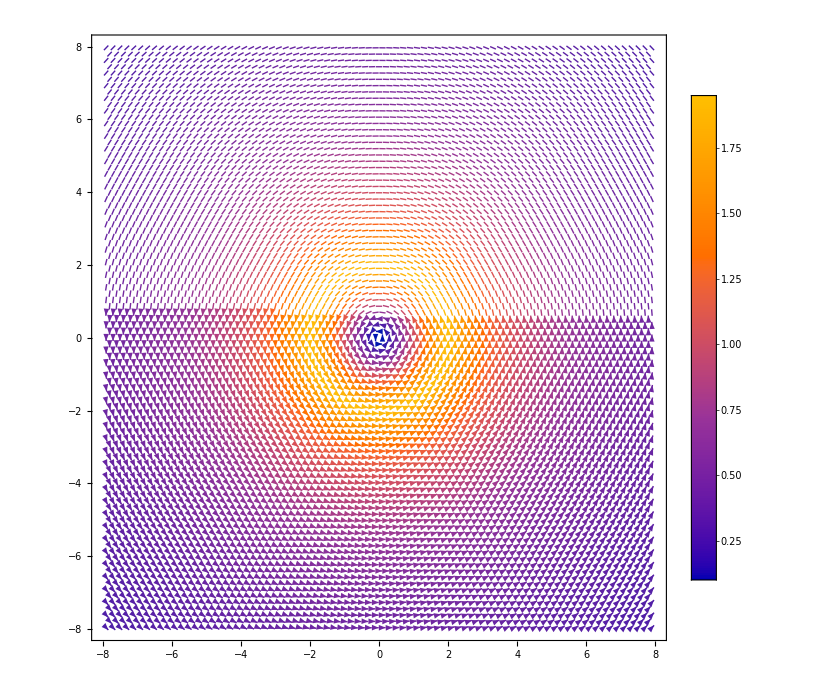

```mathematica
VectorPlot[AC[x,y,2,2],{x,-8,8},{y,-8,8},VectorPoints->80,ImageSize->700,PlotLegends->Automatic]
```